$Aborted

Preparing CSV export...

Part::partd: Part specification densities⟦1⟧ is longer than depth of object.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partd: Part specification densities⟦2⟧ is longer than depth of object.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Part::partd: Part specification densities⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

General::stop: Further output of Join::heads will be suppressed during this calculation.

Exported single CSV:

C:\Users\b09335eb\Documents\RWIHS_Programmes_MATLAB\Working Versions\Probability Densities\Results\analytic_CPn_density_n4_a0.100_p300_k2-150.csv

Generating plots...

Part::partd: Part specification densities⟦1⟧ is longer than depth of object.

Part::partd: Part specification densities⟦9⟧ is longer than depth of object.

Part::partd: Part specification densities⟦24⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0.,0.0015708,0.00314159,0.00471239,0.00628319,0.00785398,0.00942478,0.0109956,0.0125664,0.0141372,«991»},densities⟦1⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0015708,0.00314159,0.00471239,0.00628319,0.00785398,0.00942478,0.0109956,0.0125664,0.0141372,«991»},densities⟦9⟧} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0015708,0.00314159,0.00471239,0.00628319,0.00785398,0.00942478,0.0109956,0.0125664,0.0141372,«991»},densities⟦24⟧} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

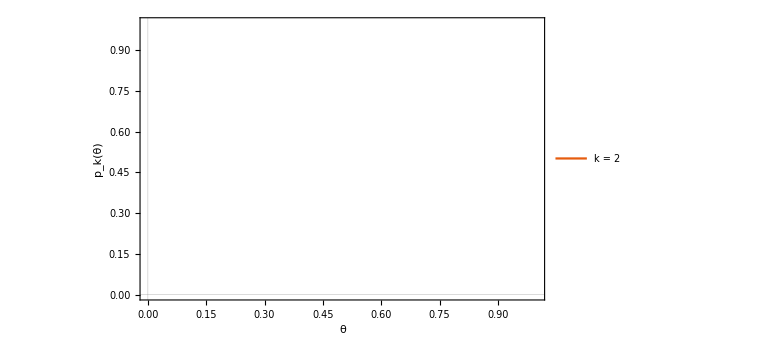

```mathematica
ClearAll["Global`*"];
$HistoryLength=0;

n=2^6;
a=0.1;
p=1500;

kList=Range[2,150];

Nθ=1000;
θGrid=N@Subdivide[0,Pi/2,Nθ];

exportDir=NotebookDirectory[]/. $Failed->Directory[];

f[θ_?NumericQ,n_Integer,a_?NumericQ,k_?NumericQ,p_Integer]:=2 Sin[θ]^(2 n-3) Cos[θ]*Sum[(2 m+n-1) Binomial[m+n-2,n-2]*(JacobiP[m,n-2,0,Cos[2 a]]/JacobiP[m,n-2,0,1])^k*JacobiP[m,n-2,0,Cos[2 θ]],{m,0,p}];

densities=Table[Module[{k=kList[[i]]},N[(f[#,n,a,k,p])&/@θGrid]],{i,Length[kList]}];

Print["Preparing CSV export..."];

exportMatrix=Table[Join[{kList[[i]]},densities[[i]]],{i,Length[kList]}];

header=Join[{"k"},θGrid];
csvTable=Prepend[exportMatrix,header];

kMin=Min[kList];
kMax=Max[kList];

aStr=StringReplace[ToString@NumberForm[a,{Infinity,3},NumberPadding->{"","0"}]," "->""];

outBase=FileNameJoin[{exportDir,"analytic_CPn_density_"<>"n"<>ToString[n]<>"_a"<>aStr<>"_p"<>ToString[p]<>"_k"<>ToString[kMin]<>"-"<>ToString[kMax]}];

outFile=outBase<>".csv";

Export[outFile,csvTable,"CSV"];

Print["Exported single CSV:"];
Print["  ",outFile];
Print["Generating plots..."];

kPlot={2, 10, 25, 50, 100, 150};
kPlot=Select[kPlot,MemberQ[kList,#]&];

idxForK=AssociationThread[kList->Range[Length[kList]]];

plotCurves=Table[densities[[idxForK[k]]],{k,kPlot}];

transitionPlot=ListLinePlot[Transpose/@({θGrid,#}&/@plotCurves),PlotRange->All,Frame->True,FrameLabel->{"θ","p_k(θ)"},PlotLegends->(Row[{"k = ",#}]&/@kPlot),ImageSize->Large,PlotTheme->"Scientific"];

Print[transitionPlot];
```